```mathematica
Quit[];
```

## Dynamic model of spring-loaded double pendulum with virtual pivot point (VPP)

System parameters: g,m, J, k, lo, d, and r

Generalized coordinates: α, θ, and l

```mathematica
α=q1[t];
θ=q2[t];
l=q3[t];

(*Other coordinates in terms of q*)
x=-l Sin[α]-d Sin[θ];
y=l Cos[α]+d Cos[θ];

xVPP=x-r Sin[θ];
yVPP=y+r Cos[θ];

γ=FullSimplify[ArcCos[(l^2+xVPP^2+yVPP^2-(r+d)^2)/(2 l Sqrt[xVPP^2+yVPP^2])]];
tanγ=FullSimplify[Tan[γ]];(*Doesn't fully simplify for some reason!*)
tanγ=((r+d) Sin[α-θ])/((r+d) Cos[α-θ]+l);
tanγapprox=((r+d)*(α-θ))/((r+d) *(1-α+θ)+l);
```

Generalized velocities: dα/dt, dθ/dt, and dl/dt

```mathematica
αdot=D[α,t];
θdot=D[θ,t];
ldot=D[l,t];

(*Other velocities in terms of q*)
xdot=D[x,t];
ydot=D[y,t];
```

Lagrangian

```mathematica
KE=First[Flatten[1/2 m{{xdot},{ydot}}ᵀ.{{xdot},{ydot}}+1/2 J θdot^2]];(*kinetic energy*)
PE=m g y+1/2 k (l-lo)^2;(*potential energy*)
L=KE-PE;
```

Euler-Lagrange equations

```mathematica
ELα=FullSimplify[D[D[L,αdot],t]-D[L,α]]==0;
ELθ=FullSimplify[D[D[L,θdot],t]-D[L,θ]]==τ;
ELl=FullSimplify[D[D[L,ldot],t]-D[L,l]]==0;

fx=FullSimplify[Flatten[Solve[{ELα,ELθ,ELl},{q1''[t],q2''[t],q3''[t]}]][[1]]][[2]]/.{q1[t]->a,q1'[t]->adot,q1''[t]->addot,q2[t]->th,q2'[t]->thdot,q2''[t]->thddot,q3[t]->ell,q3'[t]->elldot,q3''[t]->ellddot};
gx=FullSimplify[Flatten[Solve[{ELα,ELθ,ELl},{q1''[t],q2''[t],q3''[t]}]][[2]]][[2]]/.{q1[t]->a,q1'[t]->adot,q1''[t]->addot,q2[t]->th,q2'[t]->thdot,q2''[t]->thddot,q3[t]->ell,q3'[t]->elldot,q3''[t]->ellddot};
hx=FullSimplify[Flatten[Solve[{ELα,ELθ,ELl},{q1''[t],q2''[t],q3''[t]}]][[3]]][[2]]/.{q1[t]->a,q1'[t]->adot,q1''[t]->addot,q2[t]->th,q2'[t]->thdot,q2''[t]->thddot,q3[t]->ell,q3'[t]->elldot,q3''[t]->ellddot};
```

```mathematica
(*Readable output*)
Print["Equations of motion:"];
Print["α̈ = ",FullSimplify[fx/.{a->"α",adot->"α̇",th->"θ",thdot->"θ̇",ell->"l",elldot->"l̇"}]];
Print["θ̈ = ",FullSimplify[gx/.{a->"α",adot->"α̇",th->"θ",thdot->"θ̇",ell->"l",elldot->"l̇"}]];
Print["l̈ = ",FullSimplify[hx/.{a->"α",adot->"α̇",th->"θ",thdot->"θ̇",ell->"l",elldot->"l̇"}]];
```

Equations of motion:

α̈ = (J (-2 l̇ α̇+g Sin[α]-(θ̇)^2 d Sin[α-θ])-d Cos[α-θ] (τ+d k (l-lo) Sin[α-θ]))/(l J)

θ̈ = (τ+d k (l-lo) Sin[α-θ])/J

l̈ = (2 J k (-l+lo)+(2 l (α̇)^2 J-l d^2 k+d^2 k lo) m-2 g J m Cos[α]+d m (2 (θ̇)^2 J Cos[α-θ]+d k (l-lo) Cos[2 (α-θ)]-2 τ Sin[α-θ]))/(2 J m)

Linearization and stability analysis

### Find equilibria

```mathematica
equilibria=Solve[{adot==0,(fx/.τ->0)==0,thdot==0,(gx/.τ->0)==0,elldot==0,(hx/.τ->0)==0},{a,adot,th,thdot,ell,elldot}];
Print["equilibrium 1: ",equilibria[[1]]]; 
Print["equilibrium 2: ",equilibria[[2]]];
Print["equilibrium 3: ",equilibria[[3]]];
Print["equilibrium 4: ",equilibria[[4]]];
```

equilibrium 1: {adot→0,thdot→0,ell→(k lo-g m)/k,elldot→0,a→ConditionalExpression[2 π C[1],C[1]∈Integers],th→ConditionalExpression[-2 π C[2],C[2]∈Integers]}

equilibrium 2: {adot→0,thdot→0,ell→(k lo-g m)/k,elldot→0,a→ConditionalExpression[2 π C[1],C[1]∈Integers],th→ConditionalExpression[-π-2 π C[2],C[2]∈Integers]}

equilibrium 3: {adot→0,thdot→0,ell→(k lo+g m)/k,elldot→0,a→ConditionalExpression[π+2 π C[1],C[1]∈Integers],th→ConditionalExpression[-2 π C[2],C[2]∈Integers]}

equilibrium 4: {adot→0,thdot→0,ell→(k lo+g m)/k,elldot→0,a→ConditionalExpression[π+2 π C[1],C[1]∈Integers],th→ConditionalExpression[-π-2 π C[2],C[2]∈Integers]}

```mathematica
(*Choose the operating point to be "upright" and "balanced"*)
αlin=0;
αdotlin=0;
θlin=0;
θdotlin=0;
llin=lo-(m g)/k;
llindot=0;

(*Affine terms*)
FullSimplify[fx/.{a->αlin,adot->αdotlin,th->θlin,thdot->θdotlin,ell->llin,elldot->llindot,τ->0}]
FullSimplify[gx/.{a->αlin,adot->αdotlin,th->θlin,thdot->θdotlin,ell->llin,elldot->llindot,τ->0}]
FullSimplify[hx/.{a->αlin,adot->αdotlin,th->θlin,thdot->θdotlin,ell->llin,elldot->llindot,τ->0}]

(*Jacobian*)
J21=D[fx,a]/.{a->αlin,adot->αdotlin,th->θlin,thdot->θdotlin,ell->llin,elldot->llindot,τ->0};
J22=D[fx,adot]/.{a->αlin,adot->αdotlin,th->θlin,thdot->θdotlin,ell->llin,elldot->llindot,τ->0};
J23=D[fx,th]/.{a->αlin,adot->αdotlin,th->θlin,thdot->θdotlin,ell->llin,elldot->llindot,τ->0};
J24=D[fx,thdot]/.{a->αlin,adot->αdotlin,th->θlin,thdot->θdotlin,ell->llin,elldot->llindot,τ->0};
J25=D[fx,ell]/.{a->αlin,adot->αdotlin,th->θlin,thdot->θdotlin,ell->llin,elldot->llindot,τ->0};
J26=D[fx,elldot]/.{a->αlin,adot->αdotlin,th->θlin,thdot->θdotlin,ell->llin,elldot->llindot,τ->0};

J41=D[gx,a]/.{a->αlin,adot->αdotlin,th->θlin,thdot->θdotlin,ell->llin,elldot->llindot,τ->0};
J42=D[gx,adot]/.{a->αlin,adot->αdotlin,th->θlin,thdot->θdotlin,ell->llin,elldot->llindot,τ->0};
J43=D[gx,th]/.{a->αlin,adot->αdotlin,th->θlin,thdot->θdotlin,ell->llin,elldot->llindot,τ->0};
J44=D[gx,thdot]/.{a->αlin,adot->αdotlin,th->θlin,thdot->θdotlin,ell->llin,elldot->llindot,τ->0};
J45=D[gx,ell]/.{a->αlin,adot->αdotlin,th->θlin,thdot->θdotlin,ell->llin,elldot->llindot,τ->0};
J46=D[gx,elldot]/.{a->αlin,adot->αdotlin,th->θlin,thdot->θdotlin,ell->llin,elldot->llindot,τ->0};

J61=D[hx,a]/.{a->αlin,adot->αdotlin,th->θlin,thdot->θdotlin,ell->llin,elldot->llindot,τ->0};
J62=D[hx,adot]/.{a->αlin,adot->αdotlin,th->θlin,thdot->θdotlin,ell->llin,elldot->llindot,τ->0};
J63=D[hx,th]/.{a->αlin,adot->αdotlin,th->θlin,thdot->θdotlin,ell->llin,elldot->llindot,τ->0};
J64=D[hx,thdot]/.{a->αlin,adot->αdotlin,th->θlin,thdot->θdotlin,ell->llin,elldot->llindot,τ->0};
J65=D[hx,ell]/.{a->αlin,adot->αdotlin,th->θlin,thdot->θdotlin,ell->llin,elldot->llindot,τ->0};
J66=D[hx,elldot]/.{a->αlin,adot->αdotlin,th->θlin,thdot->θdotlin,ell->llin,elldot->llindot,τ->0};

jacobian=FullSimplify[{{0,1,0,0,0,0},{J21,J22,J23,J24,J25,J26},{0,0,0,1,0,0},{J41,J42,J43,J44,J45,J46},{0,0,0,0,0,1},{J61,J62,J63,J64,J65,J66}}];
Print["Jacobian = ",MatrixForm[jacobian]];

B1=0;
B2=D[fx,τ]/.{a->αlin,adot->αdotlin,th->θlin,thdot->θdotlin,ell->llin,elldot->llindot,τ->0};
B3=0;
B4=D[gx,τ]/.{a->αlin,adot->αdotlin,th->θlin,thdot->θdotlin,ell->llin,elldot->llindot,τ->0};
B5=0;
B6=D[hx,τ]/.{a->αlin,adot->αdotlin,th->θlin,thdot->θdotlin,ell->llin,elldot->llindot,τ->0};

Bmatrix=FullSimplify[{{B1},{B2},{B3},{B4},{B5},{B6}}];
Print["B matix = ",MatrixForm[Bmatrix]];

(*Eigenvalues*)
{λ1,λ2,λ3,λ4,λ5,λ6}=FullSimplify[Eigenvalues[FullSimplify[jacobian]]];
gp=9.81;
mp=5;
Jp=0.25;
kp=100;
lop=0.5;
dp=0.2;
rp=0.2;
τp=0;
Print["Eigenvalues:"];
Print["λ1 = ",FullSimplify[λ1]];
Print["λ2 = ",FullSimplify[λ2]];
Print["λ3 = ",FullSimplify[λ3]];
Print["λ4 = ",FullSimplify[λ4]];
Print["λ5 = ",FullSimplify[λ5]];
Print["λ6 = ",FullSimplify[λ6]];

Print["Eigenvalues as functions of stiffness k and distance r:"];
(*Print["λ1 = ",FullSimplify[λ1]/.{g->gp,m->mp,J->Jp,lo->lop,d->dp,τ->τp}];
Print["λ2 = ",FullSimplify[λ2]/.{g->gp,m->mp,J->Jp,lo->lop,d->dp,τ->τp}];
Print["λ3 = ",FullSimplify[λ3]/.{g->gp,m->mp,J->Jp,lo->lop,d->dp,τ->τp}];
Print["λ4 = ",FullSimplify[λ4]/.{g->gp,m->mp,J->Jp,lo->lop,d->dp,τ->τp}];
Print["λ5 = ",FullSimplify[λ5]/.{g->gp,m->mp,J->Jp,lo->lop,d->dp,τ->τp}];
Print["λ6 = ",FullSimplify[λ6]/.{g->gp,m->mp,J->Jp,lo->lop,d->dp,τ->τp}];*)

(*Plot real parts of eigenvalues vs stiffness k*)
(*reλ1=Re[λ1/.{g->gp,m->mp,J->Jp,lo->lop,d->dp,r->rp,τ->τp}];
reλ2=Re[λ2/.{g->gp,m->mp,J->Jp,lo->lop,d->dp,r->rp,τ->τp}];
reλ3=Re[λ3/.{g->gp,m->mp,J->Jp,lo->lop,d->dp,r->rp,τ->τp}];
reλ4=Re[λ4/.{g->gp,m->mp,J->Jp,lo->lop,d->dp,r->rp,τ->τp}];
reλ5=Re[λ5/.{g->gp,m->mp,J->Jp,lo->lop,d->dp,r->rp,τ->τp}];
reλ6=Re[λ6/.{g->gp,m->mp,J->Jp,lo->lop,d->dp,r->rp,τ->τp}];
Plot[{reλ1,reλ2,reλ3,reλ4,reλ5,reλ6},{k,0,100},AxesLabel->{"k","Re[λ]"},PlotLabel->"Re[λ] vs k",PlotLegends->{"Re[λ1]","Re[λ2]","Re[λ3]","Re[λ4]","Re[λ5]","Re[λ6]"}]*)

(*Plot imaginary parts of eigenvalues vs stiffness k*)
(*imλ1=Im[λ1/.{g->gp,m->mp,J->Jp,lo->lop,d->dp,r->rp,τ->τp}];
imλ2=Im[λ2/.{g->gp,m->mp,J->Jp,lo->lop,d->dp,r->rp,τ->τp}];
imλ3=Im[λ3/.{g->gp,m->mp,J->Jp,lo->lop,d->dp,r->rp,τ->τp}];
imλ4=Im[λ4/.{g->gp,m->mp,J->Jp,lo->lop,d->dp,r->rp,τ->τp}];
imλ5=Im[λ5/.{g->gp,m->mp,J->Jp,lo->lop,d->dp,r->rp,τ->τp}];
imλ6=Im[λ6/.{g->gp,m->mp,J->Jp,lo->lop,d->dp,r->rp,τ->τp}];
Plot[{imλ1,imλ2,imλ3,imλ4,imλ5,imλ6},{k,0,100},AxesLabel->{"k","Im[λ]"},PlotLabel->"Im[λ] vs k",PlotLegends->{"Im[λ1]","Im[λ2]","Im[λ3]","Im[λ4]","Im[λ5]","Im[λ6]"}]*)

(*Make 3D plots of real parts of eigenvalues*)
(*Plot3D[Re[λ1/.{g->gp,m->mp,J->Jp,lo->lop,d->dp,τ->τp}],{k,0,100},{r,0,0.5},PlotLabel->"Re[λ1] vs k and r"]
Plot3D[Re[λ2/.{g->gp,m->mp,J->Jp,lo->lop,d->dp,τ->τp}],{k,0,100},{r,0,0.5},PlotLabel->"Re[λ2] vs k and r"]
Plot3D[Re[λ3/.{g->gp,m->mp,J->Jp,lo->lop,d->dp,τ->τp}],{k,0,100},{r,0,0.5},PlotLabel->"Re[λ3] vs k and r"]
Plot3D[Re[λ4/.{g->gp,m->mp,J->Jp,lo->lop,d->dp,τ->τp}],{k,0,100},{r,0,0.5},PlotLabel->"Re[λ4] vs k and r"]
Plot3D[Re[λ5/.{g->gp,m->mp,J->Jp,lo->lop,d->dp,τ->τp}],{k,0,100},{r,0,0.5},PlotLabel->"Re[λ5] vs k and r"]
Plot3D[Re[λ6/.{g->gp,m->mp,J->Jp,lo->lop,d->dp,τ->τp}],{k,0,100},{r,0,0.5},PlotLabel->"Re[λ6] vs k and r"]*)

(*Make 3D plots of imaginary parts of eigenvalues*)
(*Plot3D[Im[λ1/.{g->gp,m->mp,J->Jp,lo->lop,d->dp,τ->τp}],{k,0,100},{r,0,0.5},PlotLabel->"Im[λ1] vs k and r"]
Plot3D[Im[λ2/.{g->gp,m->mp,J->Jp,lo->lop,d->dp,τ->τp}],{k,0,100},{r,0,0.5},PlotLabel->"Im[λ2] vs k and r"]
Plot3D[Im[λ3/.{g->gp,m->mp,J->Jp,lo->lop,d->dp,τ->τp}],{k,0,100},{r,0,0.5},PlotLabel->"Im[λ3] vs k and r"]
Plot3D[Im[λ4/.{g->gp,m->mp,J->Jp,lo->lop,d->dp,τ->τp}],{k,0,100},{r,0,0.5},PlotLabel->"Im[λ4] vs k and r"]
Plot3D[Im[λ5/.{g->gp,m->mp,J->Jp,lo->lop,d->dp,τ->τp}],{k,0,100},{r,0,0.5},PlotLabel->"Im[λ5] vs k and r"]
Plot3D[Im[λ6/.{g->gp,m->mp,J->Jp,lo->lop,d->dp,τ->τp}],{k,0,100},{r,0,0.5},PlotLabel->"Im[λ6] vs k and r"]*)
(*Print["λ1 = ",λ1/.{g->gp,m->mp,J->Jp,k->kp,lo->lop,d->dp,r->rp,τ->τp}];
Print["λ2 = ",λ2/.{g->gp,m->mp,J->Jp,k->kp,lo->lop,d->dp,r->rp,τ->τp}];
Print["λ3 = ",λ3/.{g->gp,m->mp,J->Jp,k->kp,lo->lop,d->dp,r->rp,τ->τp}];
Print["λ4 = ",λ4/.{g->gp,m->mp,J->Jp,k->kp,lo->lop,d->dp,r->rp,τ->τp}];
Print["λ5 = ",λ5/.{g->gp,m->mp,J->Jp,k->kp,lo->lop,d->dp,r->rp,τ->τp}];
Print["λ6 = ",λ6/.{g->gp,m->mp,J->Jp,k->kp,lo->lop,d->dp,r->rp,τ->τp}];*)
```

0

0

0

Jacobian = (0 | 1 | 0 | 0 | 0 | 0
(g k (J+d^2 m))/(J (k lo-g m)) | 0 | -(d^2 g k m)/(J k lo-g J m) | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
-(d g m)/J | 0 | (d g m)/J | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | -k/m | 0)

B matix = (0
-(d k)/(J k lo-g J m)
0
1/J
0
0)

Eigenvalues:

λ1 = (ⅈ √k)/(√m)

λ2 = -(ⅈ √k)/(√m)

λ3 = -(√(g J m^2 (k lo-g m) (J k+d m (k (d+lo)-g m)+√(J^2 k^2+d^2 m^2 (k (d+lo)-g m)^2+2 d J k m (d k-k lo+g m)))))/(√2 J m (-k lo+g m))

λ4 = (√(g J m^2 (k lo-g m) (J k+d m (k (d+lo)-g m)+√(J^2 k^2+d^2 m^2 (k (d+lo)-g m)^2+2 d J k m (d k-k lo+g m)))))/(√2 J m (-k lo+g m))

λ5 = -(√(g J m^2 (-k lo+g m) (-J k+d m (-k (d+lo)+g m)+√(J^2 k^2+d^2 m^2 (k (d+lo)-g m)^2+2 d J k m (d k-k lo+g m)))))/(√2 J m (-k lo+g m))

λ6 = (√(g J m^2 (-k lo+g m) (-J k+d m (-k (d+lo)+g m)+√(J^2 k^2+d^2 m^2 (k (d+lo)-g m)^2+2 d J k m (d k-k lo+g m)))))/(√2 J m (-k lo+g m))

Eigenvalues as functions of stiffness k and distance r:

VPP feedback controller design

This doesn’t work yet! It’s based on a nonlinear control law from a Nature paper on walking.

```mathematica
xvl=-ell a -(d+r)th;
yvl=ell (1-a)+(d+r) (1-th);
cosγl=FullSimplify[(ell^2+xvl^2+yvl^2-(d+r)^2)/(2 ell Sqrt[xvl^2+yvl^2])]
tanγl=FullSimplify[Expand[Tan[ArcCos[cosγl]]]]/.{a->"α",adot->"α̇",th->"θ",thdot->"θ̇",ell->"l",elldot->"l̇"}
```

(ell (ell+(-1+a) (-d+a ell)+r-a r)-(d+r) (d+ell-2 a ell+r) th+(d+r)^2 th^2)/(ell √((d+ell-a ell+r-(d+r) th)^2+(a ell+(d+r) th)^2))

(l √((l-l α+d+r-θ (d+r))^2+(l α+θ (d+r))^2) √(1-((θ^2 (d+r)^2-θ (d+r) (l-2 l α+d+r)+l (l+(-1+α) (l α-d)+r-α r))^2)/(l^2 ((l-l α+d+r-θ (d+r))^2+(l α+θ (d+r))^2))))/(θ^2 (d+r)^2-θ (d+r) (l-2 l α+d+r)+l (l+(-1+α) (l α-d)+r-α r))

## Reachability

### Reachability of the full system

```mathematica
A=jacobian;
B=Bmatrix;

Wr=FullSimplify[Join[B,Join[A.B, Join[A.A.B,Join[A.A.A.B,Join[A.A.A.A.B,A.A.A.A.A.B,2],2],2],2],2]];
Print["A = ",MatrixForm[A]];
Print["B = ",MatrixForm[B]];
Print["W_r = ",MatrixForm[Wr]];
Print["det(W_r) = ",FullSimplify[Det[Wr]]];
Print["Rank(W_r) = ",MatrixRank[Wr]];
```

A = (0 | 1 | 0 | 0 | 0 | 0
(g k (J+d^2 m))/(J (k lo-g m)) | 0 | -(d^2 g k m)/(J k lo-g J m) | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
-(d g m)/J | 0 | (d g m)/J | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | -k/m | 0)

B = (0
-(d k)/(J k lo-g J m)
0
1/J
0
0)

W_r = (0 | -(d k)/(J k lo-g J m) | 0 | -(d g k (J k+d m (k (d+lo)-g m)))/(J^2 (k lo-g m)^2) | 0 | -(d g^2 k (J^2 k^2+d J k m (2 d k+k lo-g m)+d^2 m^2 (k (d+lo)-g m)^2))/(J^3 (k lo-g m)^3)
-(d k)/(J k lo-g J m) | 0 | -(d g k (J k+d m (k (d+lo)-g m)))/(J^2 (k lo-g m)^2) | 0 | -(d g^2 k (J^2 k^2+d J k m (2 d k+k lo-g m)+d^2 m^2 (k (d+lo)-g m)^2))/(J^3 (k lo-g m)^3) | 0
0 | 1/J | 0 | (d g m (k (d+lo)-g m))/(J^2 (k lo-g m)) | 0 | (d^2 g^2 m (J k^2+m (k (d+lo)-g m)^2))/(J^3 (k lo-g m)^2)
1/J | 0 | (d g m (k (d+lo)-g m))/(J^2 (k lo-g m)) | 0 | (d^2 g^2 m (J k^2+m (k (d+lo)-g m)^2))/(J^3 (k lo-g m)^2) | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

det(W_r) = 0

Rank(W_r) = 4

### Reachability of reduced system - ignore spring length and d/dt of spring length

```mathematica
Ared={{A[[1,1]],A[[1,2]],A[[1,3]],A[[1,4]]},{A[[2,1]],A[[2,2]],A[[2,3]],A[[2,4]]},{A[[3,1]],A[[3,2]],A[[3,3]],A[[3,4]]},{A[[4,1]],A[[4,2]],A[[4,3]],A[[4,4]]}};
Bred={{B[[1,1]]},{B[[2,1]]},{B[[3,1]]},{B[[4,1]]}};
Print["Reduced A matrix = ",MatrixForm[Ared]];
Print["Reduced B matrix = ",MatrixForm[Bred]];
Wrred=FullSimplify[Join[Bred,Join[Ared.Bred, Join[Ared.Ared.Bred,Ared.Ared.Ared.Bred,2],2],2]];(*Here I am forming the "controllability matrix"*)
Print["Reduced W_(r, red) = ",MatrixForm[Wrred]];
Print["det(W_(r, red)) = ",FullSimplify[Det[Wrred]]];(*A nonzero determinant means the system (or here, the reduced system) is "reachable"*)
Print["Rank(W_(r, red)) = ",MatrixRank[Wrred]];(*A rank equal to the dimension of the system's state means the system is controllable. Here, the "system" is actually the reduced system explained above, so we want the rank to be 4.*)
```

Reduced A matrix = (0 | 1 | 0 | 0
(g k (J+d^2 m))/(J (k lo-g m)) | 0 | -(d^2 g k m)/(J k lo-g J m) | 0
0 | 0 | 0 | 1
-(d g m)/J | 0 | (d g m)/J | 0)

Reduced B matrix = (0
-(d k)/(J k lo-g J m)
0
1/J)

Reduced W_(r, red) = (0 | -(d k)/(J k lo-g J m) | 0 | -(d g k (J k+d m (k (d+lo)-g m)))/(J^2 (k lo-g m)^2)
-(d k)/(J k lo-g J m) | 0 | -(d g k (J k+d m (k (d+lo)-g m)))/(J^2 (k lo-g m)^2) | 0
0 | 1/J | 0 | (d g m (k (d+lo)-g m))/(J^2 (k lo-g m))
1/J | 0 | (d g m (k (d+lo)-g m))/(J^2 (k lo-g m)) | 0)

det(W_(r, red)) = (d^2 g^2 k^4)/(J^4 (k lo-g m)^4)

Rank(W_(r, red)) = 4

### Stabilization of reachable subsystem by state feedback

This also doesn’t work yet! Instead, look at the next section about LQR. Basically there are two alternatives for stabilizing the system.
	You can solve the “pole placement problem”, which often involves you deciding where you want the closed loop poles to be (and how do you know where you want them to be? It’s kind of arbitrary)
	Or, you can choose “optimal” pole locations, by implementing an LQR controller, where “optimality” is determined by your Q and R matrices.
		That is an “infinite horizon” LQR controller, so it’s a little different from the finite horizon trajectory optimization we did in Todd’s class. Specifically, it’s easier, and Mathematica and MATLAB have software to do it for you.
Reference: http://www.cds.caltech.edu/~murray/books/AM05/pdf/am06-statefbk_16Sep06.pdf

```mathematica
Cred={{1,1,1,1}};
Dred={{0}};
Kred={{k1,k2,k3,k4}};

gs=9.81;
ms=5;
Js=0.25;
ks=1000;
los=1;
ds=0.4;
rs=0.6;

Print["Open loop characteristic polynomial: ",FullSimplify[Det[s IdentityMatrix[4]-Ared]]]
Print["Open loop poles are the roots of the characteristic polynomial."]
polesred=Solve[FullSimplify[Det[s IdentityMatrix[4]-Ared]]==0,s];
Print["Poles: ",polesred];
Print["Particular poles: ",polesred/.{g->gs,m->ms,J->Js,k->ks,lo->los,d->ds,r->rs}];
Print["Check for non-minimum phase behavior by looking at open-loop zeros. NMP if zeros in RHP."]
Print["Polynomial associated with zeros: ",FullSimplify[Det[Join[Join[s IdentityMatrix[4]-Ared,-Bred,2],Join[Cred,Dred,2],1]]]];
zerosred=Solve[FullSimplify[Det[Join[Join[s IdentityMatrix[4]-Ared,-Bred,2],Join[Cred,Dred,2],1]]]==0,s];
Print["Zeros: ",zerosred];
Print["particular zeros: ",zerosred/.{g->gs,m->ms,J->Js,k->ks,lo->los,d->ds,r->rs}];
OLTF=FullSimplify[Expand[FullSimplify[Det[Join[Join[s IdentityMatrix[4]-Ared,-Bred,2],Join[Cred,Dred,2],1]]]]/Expand[FullSimplify[Det[s IdentityMatrix[4]-Ared]]]];
Print["Open loop TF: ",OLTF];
clcharpoly=FullSimplify[Det[s IdentityMatrix[4]-Ared+Bred.Kred]]/.{g->gs,m->ms,J->Js,k->ks,lo->los,d->ds,r->rs}
(*Print["Closed loop poles: ",FullSimplify[Solve[clcharpoly==0,s]]];*)

(*krred=FullSimplify[-1/(Cred.Inverse[Ared-Bred.Kred].Bred)];*)
```

Characteristic polynomial: (d g^2 k m-g (J k+d m (k (d+lo)-g m)) s^2+J (k lo-g m) s^4)/(J (k lo-g m))

Open loop poles are the roots of the characteristic polynomial.

Poles: {{s→-√(-(g J k)/(2 (-J k lo+g J m))-(d^2 g k m)/(2 (-J k lo+g J m))-(d g k lo m)/(2 (-J k lo+g J m))+(d g^2 m^2)/(2 (-J k lo+g J m))-(√(4 d g^2 k m (-J k lo+g J m)+(g J k+d^2 g k m+d g k lo m-d g^2 m^2)^2))/(2 (-J k lo+g J m)))},{s→√(-(g J k)/(2 (-J k lo+g J m))-(d^2 g k m)/(2 (-J k lo+g J m))-(d g k lo m)/(2 (-J k lo+g J m))+(d g^2 m^2)/(2 (-J k lo+g J m))-(√(4 d g^2 k m (-J k lo+g J m)+(g J k+d^2 g k m+d g k lo m-d g^2 m^2)^2))/(2 (-J k lo+g J m)))},{s→-√(-(g J k)/(2 (-J k lo+g J m))-(d^2 g k m)/(2 (-J k lo+g J m))-(d g k lo m)/(2 (-J k lo+g J m))+(d g^2 m^2)/(2 (-J k lo+g J m))+(√(4 d g^2 k m (-J k lo+g J m)+(g J k+d^2 g k m+d g k lo m-d g^2 m^2)^2))/(2 (-J k lo+g J m)))},{s→√(-(g J k)/(2 (-J k lo+g J m))-(d^2 g k m)/(2 (-J k lo+g J m))-(d g k lo m)/(2 (-J k lo+g J m))+(d g^2 m^2)/(2 (-J k lo+g J m))+(√(4 d g^2 k m (-J k lo+g J m)+(g J k+d^2 g k m+d g k lo m-d g^2 m^2)^2))/(2 (-J k lo+g J m)))}}

Particular poles: {{s→-10.7122},{s→10.7122},{s→-2.65617},{s→2.65617}}

Check for non-minimum phase behavior by looking at open-loop zeros. NMP if zeros in RHP.

Polynomial associated with zeros: -((1+s) (g k+(d k-k lo+g m) s^2))/(J (k lo-g m))

Zeros: {{s→-1},{s→-(√g √k)/(√(-d k+k lo-g m))},{s→(√g √k)/(√(-d k+k lo-g m))}}

particular zeros: {{s→-1},{s→-4.21967},{s→4.21967}}

Open loop TF: ((1+s) (g k+(d k-k lo+g m) s^2))/(-d g^2 k m+g (J k+d m (k (d+lo)-g m)) s^2+J (-k lo+g m) s^4)

0.00420632 (192.472 (1000+5 s^2)+1000 s^2 (k3+(k4+0.25 s) s-0.4 (k1+k2 s))-9.81 (5 s^2 (k3+(k4+0.25 s) s)+1000 (k3+s (k4+3.05 s))))

LQR control of the linearized system

See my block of text in the previous section.

```mathematica
ssmred=StateSpaceModel[{Ared,Bred,Cred,Dred}/.{g->gs,m->ms,J->Js,k->ks,lo->los,d->ds,r->rs}]
Qred=DiagonalMatrix[{1,1,1,1}];
Rred=DiagonalMatrix[{1}];
Kred=LQRegulatorGains[ssmred,{Qred,Rred}];
Print["LQR gains: ",Kred];
```

0100043.32720-33.01120-1.6825300010-78.48078.4804.11110StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1141FalseFalseFalseAutomaticNoneAutomatic

LQR gains: {{-214.096,-60.2479,-0.0254677,-18.5457}}

Numerical simulation of linearized system with LQR

Doesn’t work yet!

```mathematica
EOMred=ξ'[t]==Ared.ξ[t]/.{g->gs,m->ms,J->Js,k->ks,lo->los,d->ds,r->rs};
(*EOMred=ξ'[t]==Ared.ξ[t]+Bred.(Kred.ξ[t])/.{g->gs,m->ms,J->Js,k->ks,lo->los,d->ds,r->rs};*)
ICred=ξ[0]=={{Pi/6},{0},{-Pi/6},{0}};
solred=NDSolve[{EOMred,ICred},{ξ},{t,0,10}];
Plot[Evaluate[ξ[t]/.solred],{t,0,10},PlotStyle->Automatic]
```

-Graphics-

Numerical simulation of nonlinear system

Doesn’t work yet!

{-214.096 q1[t]-0.0254677 q2[t]-60.2479 q1'[t]-18.5457 q2'[t]}

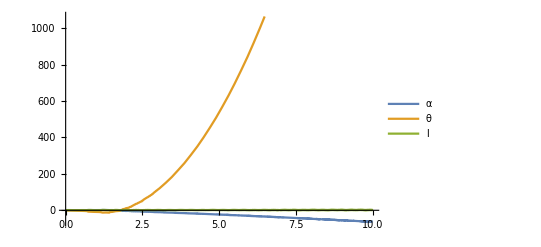

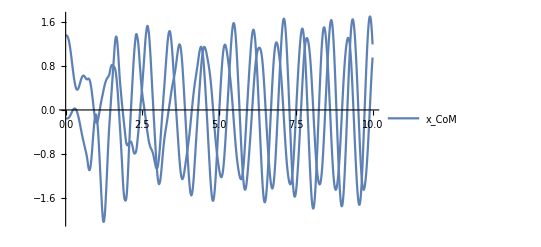

$Aborted

-Graphics-

$Aborted

```mathematica
gs=9.81;
ms=5;
Js=0.25;
ks=1000;
los=1;
ds=0.4;
rs=0.6;

τs=Join[Flatten[Kred],{0,0},1].{{q1[t]},{q1'[t]},{q2[t]},{q2'[t]},{q3[t]},{q3'[t]}}

EOM={α''[t]==fx,θ''[t]==gx,l''[t]==hx}/.{g->gs,m->ms,J->Js,k->ks,lo->los,d->ds,r->rs,τ->τs};
ICs={q1[0]==Pi/12,q1'[0]==0,q2[0]==-Pi/12,q2'[0]==0,q3[0]==los,q3'[0]==0};

sol=NDSolve[{ELα,ELθ,ELl,ICs}/.{g->gs,m->ms,J->Js,k->ks,lo->los,d->ds,r->rs,τ->τs},{q1,q2,q3},{t,0,10}];

Plot[Evaluate[{q1[t],q2[t],q3[t]}/.sol],{t,0,10},PlotStyle->Automatic,PlotLegends->{"α","θ","l"}]
Plot[Evaluate[{x,y}/.sol]/.{g->gs,m->ms,J->Js,k->ks,lo->los,d->ds,r->rs,τ->τs},{t,0,10},PlotStyle->Automatic,PlotLegends->{"x_CoM","y_CoM"}]
Plot[Evaluate[{xVPP,yVPP}/.sol]/.{g->gs,m->ms,J->Js,k->ks,lo->los,d->ds,r->rs,τ->τs},{t,0,10},PlotStyle->Automatic,PlotLegends->{"x_VPP","y_VPP"}]
Plot[Evaluate[τ/.sol]/.{g->gs,m->ms,J->Js,k->ks,lo->los,d->ds,r->rs,τ->τs},{t,0,10},PlotLegends->"τ"]

Etot=KE+PE;
Plot[Evaluate[Etot/.sol]/.{g->gs,m->ms,J->Js,k->ks,lo->los,d->ds,r->rs,τ->τs},{t,0,10},PlotLegends->"E"]
```

Animation the numerical simulation

```mathematica
xHIP=-l Sin[α]/.{g->gs,m->ms,J->Js,k->ks,lo->los,d->ds,r->rs,τ->τs};
yHIP=l Cos[α]/.{g->gs,m->ms,J->Js,k->ks,lo->los,d->ds,r->rs,τ->τs};
xCoM=x/.{g->gs,m->ms,J->Js,k->ks,lo->los,d->ds,r->rs,τ->τs};
yCoM=y/.{g->gs,m->ms,J->Js,k->ks,lo->los,d->ds,r->rs,τ->τs};
xvpp=xVPP/.{g->gs,m->ms,J->Js,k->ks,lo->los,d->ds,r->rs,τ->τs};
yvpp=yVPP/.{g->gs,m->ms,J->Js,k->ks,lo->los,d->ds,r->rs,τ->τs};
anim=Animate[Show[Graphics[{Black,PointSize[.05],Point[{{0,0}}]}],
Graphics[Line[{First[Evaluate[{0,0}/.sol]/.t->T],First[Evaluate[{xHIP,yHIP}/.sol]/.t->T]}]],Graphics[{Green,PointSize[.05],Point[Evaluate[{xHIP,yHIP}/.sol]/.t->T]}],Graphics[Line[{First[Evaluate[{xHIP,yHIP}/.sol]/.t->T],First[Evaluate[{xvpp,yvpp}/.sol]/.t->T]}]],Graphics[{Blue,PointSize[.05],Point[Evaluate[{xvpp,yvpp}/.sol]/.t->T]}],
Graphics[Line[{First[Evaluate[{xvpp,yvpp}/.sol]/.t->T],First[Evaluate[{xCoM,yCoM}/.sol]/.t->T]}]],Graphics[{Red,PointSize[.05],Point[Evaluate[{xCoM,yCoM}/.sol]/.t->T]}],PlotRange->{{-3,3},{-3,3}}],{T,0,10},AnimationDirection->Forward,AnimationRate->1]
```

Export the animation

```mathematica
Export["Documents/Research/Hop3r/Mathematica/videos/VPP.gif",Table[Show[Graphics[{Black,PointSize[.05],Point[{{0,0}}]}],
Graphics[Line[{First[Evaluate[{0,0}/.sol]/.t->T],First[Evaluate[{xHIP,yHIP}/.sol]/.t->T]}]],Graphics[{Green,PointSize[.05],Point[Evaluate[{xHIP,yHIP}/.sol]/.t->T]}],Graphics[Line[{First[Evaluate[{xHIP,yHIP}/.sol]/.t->T],First[Evaluate[{xVPP,yVPP}/.sol]/.t->T]}]],Graphics[{Blue,PointSize[.05],Point[Evaluate[{xVPP,yVPP}/.sol]/.t->T]}],
Graphics[Line[{First[Evaluate[{xVPP,yVPP}/.sol]/.t->T],First[Evaluate[{x,y}/.sol]/.t->T]}]],Graphics[{Red,PointSize[.05],Point[Evaluate[{x,y}/.sol]/.t->T]}],PlotRange->{{-3,3},{-3,3}}],{T,0,10,0.25}]];
```